## Configuration Plotting (A1, A2, H) = (0.0, 0.0, 2.0) (L=36, Mon=2×10^5)

```mathematica
Needs["VectorFieldPlots`"]
SetDirectory[NotebookDirectory[]];
ConfPlotting[file_]:=
(
list=ReadList[file,{Number,Number,Number}];
newlist=Table[{{Floor[(i-1)/36],Mod[i-1,36],0},list[[i]]},{i,36*36}];
ListVectorFieldPlot3D[newlist,ScaleFactor->1, VectorHeads->True]
)
Lx=36;Ly=36;
lab[i_,j_]:=newlist[[(j-1)*Lx+i,2]];
ipx=Table[i+1,{i,1,Lx}];ipx[[Lx]]=1;
imx=Table[i-1,{i,1,Lx}];imx[[1]]=Lx;  
ipy=Table[i+1,{i,1,Ly}];ipy[[Ly]]=1;
imy=Table[i-1,{i,1,Ly}];imy[[1]]=Ly;  
χ[i_,j_]:=(1/(8*Pi))*(lab[i,j].(lab[ipx[[i]],j]×lab[i,ipy[[j]]])+lab[i,j].(lab[imx[[i]],j]×lab[i,imy[[j]]]));
Sz[i_,j_]:=newlist[[(j-1)*Lx+i,2,3]];

k[kx_,ky_]:={kx,ky};
r[x_,y_]:={x,y};
Sk[kx_,ky_]:=Sum[lab[x,y]*Exp[-I*k[kx,ky].r[x,y]],{x,1,Lx},{y,1,Ly}];
(**)
```

T=0.10

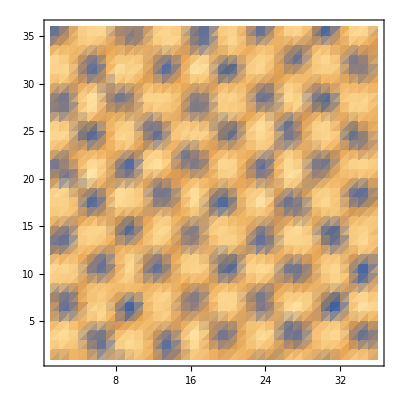
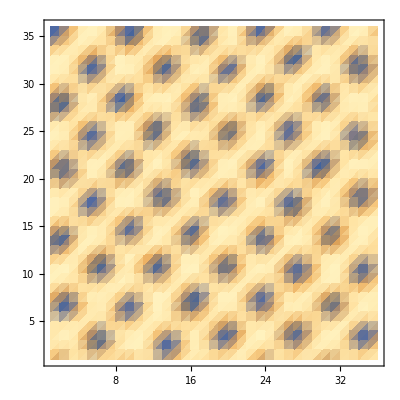
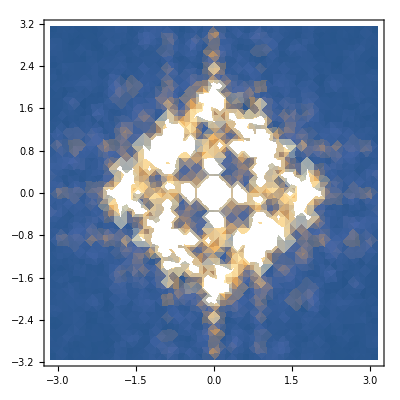
{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Text["T=0.10"]
{ConfPlotting["conf_H2.00_T0.10_dec.txt"],
ListDensityPlot[Table[χ[i,j],{i,1,Lx},{j,1,Ly}]],ListPlot3D[Table[χ[i,j],{i,1,Lx},{j,1,Ly}],PlotRange->{-0.08,0.08}],ListDensityPlot[Table[Sz[i,j],{i,1,Lx},{j,1,Ly}]],DensityPlot[Sk[i,j].Sk[-i,-j],{i,-Pi,Pi},{j,-Pi,Pi}]}
```

T=0.50

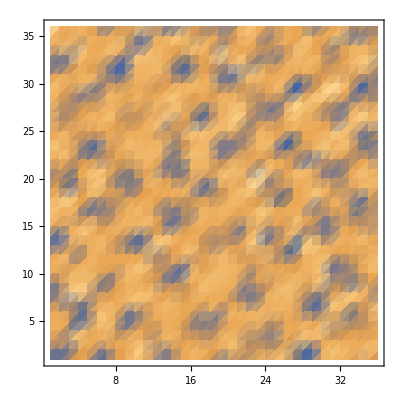
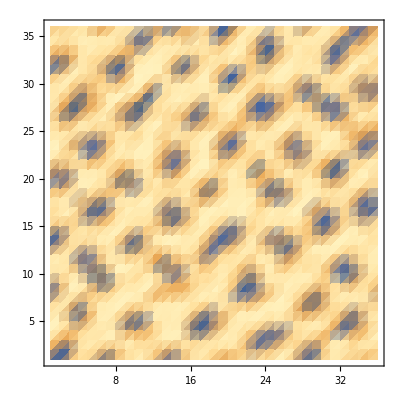
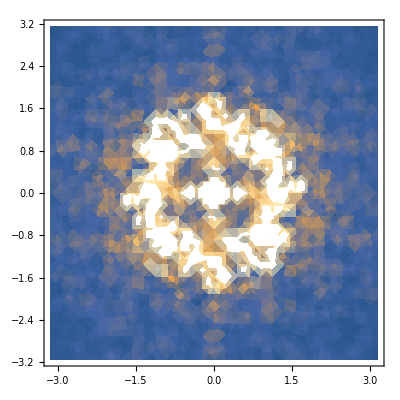
{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Text["T=0.50"]
{ConfPlotting["conf_H2.00_T0.50_dec.txt"],
ListDensityPlot[Table[χ[i,j],{i,1,Lx},{j,1,Ly}]],ListPlot3D[Table[χ[i,j],{i,1,Lx},{j,1,Ly}],PlotRange->{-0.08,0.08}],ListDensityPlot[Table[Sz[i,j],{i,1,Lx},{j,1,Ly}]],DensityPlot[Sk[i,j].Sk[-i,-j],{i,-Pi,Pi},{j,-Pi,Pi}]}
```

T=0.9

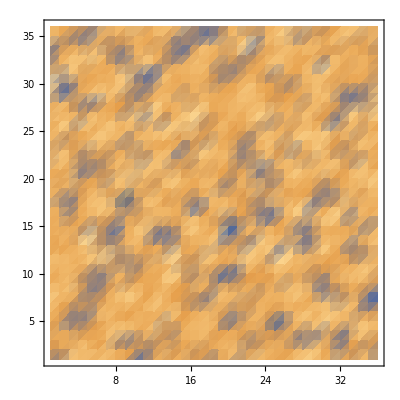
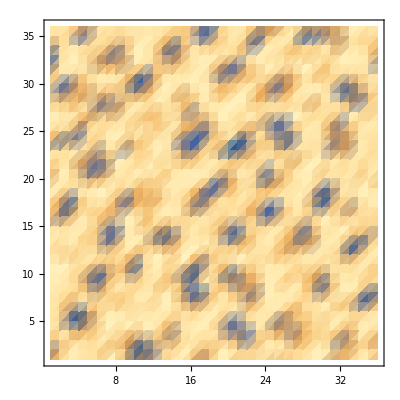
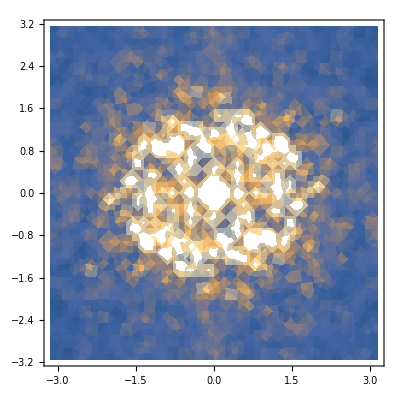
{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Text["T=0.9"]
{ConfPlotting["conf_H2.00_T0.90_dec.txt"],
ListDensityPlot[Table[χ[i,j],{i,1,Lx},{j,1,Ly}]],ListPlot3D[Table[χ[i,j],{i,1,Lx},{j,1,Ly}],PlotRange->{-0.08,0.08}],ListDensityPlot[Table[Sz[i,j],{i,1,Lx},{j,1,Ly}]],DensityPlot[Sk[i,j].Sk[-i,-j],{i,-Pi,Pi},{j,-Pi,Pi}]}
```